```mathematica
int1=Integrate[ x^2 Exp[xi x^2],{x,0,1}]
int2=Integrate[ Exp[xi x^2],{x,0,1}]
eta = 3/2 (int1 / int2 - 1/3);
Series[eta[xi],{xi,0,10}]
```

ⅇ^xi/(2 xi)-(√π Erfi[√xi])/(4 xi^(3/2))

(√π Erfi[√xi])/(2 √xi)

(3/2 (-1/3+(2 √xi (ⅇ^xi/(2 xi)-(√π Erfi[√xi])/(4 xi^(3/2))))/(√π Erfi[√xi])))[xi]

```mathematica
a1=-0.0115;
a2=0.0001344;
b1=-0.0169;
b2=0.002377;
c1=0.02019;
c2=-0.003805;
d1=0.01832;
d2=-0.005388;
e1=-0.0001432;
e2=0.003987;
f2=0.002682;
app=(a1*xi^4+b1*xi^3+c1*xi^2+d1*xi^1+e1)/(a2*xi^5+b2*xi^4+c2*xi^3+d2*xi^2+e2*xi^1+f2);
intApp=Integrate[app,xi]
```

-1.25013 Log[0.998429-1. xi]-9.01033 Log[1.95433-1. xi]-0.538693 Log[0.492869+1. xi]-1.03895 Log[1.08882+1. xi]-73.7274 Log[19.0571+1. xi]

```mathematica
0.8042
```

0.8042

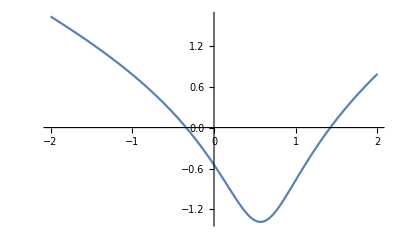

```mathematica
da=0.04 * 4.45;
Psi[Q_,f_,d_]:=0.5 * (Q*Q-Q*Q/d)+0.00436*Q+0.760281*Log[0.488312-1.14827*Q+Q*Q]-f*Q
Plot[Psi[Q,0,1.1],{Q,-2,2},PlotRange->All]
```

```mathematica
dPsidQ[Q_,f_,d_]:=Q-Q/d+0.00436+(28.1*Q-0.05178)/(9.024+21.22*Q+18.48*Q*Q)-f
D[dPsidQ[Q,0,δ],Q]
```

1-((-0.05178+28.1 Q) (21.22+36.96 Q))/((9.024+21.22 Q+18.48 Q^2)^2)+28.1/(9.024+21.22 Q+18.48 Q^2)-1/δ

```mathematica
Solve[1-((-0.05178+28.1 Q) (21.22+36.96 Q))/((9.024+21.22 Q+18.48 Q^2)^2)+28.1/(9.024+21.22 Q+18.48 Q^2)-1/δ==0,δ]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{δ→(40. (2256.+5305. Q+4620. Q^2)^2)/(8.40264×10^8+9.62231×10^8 Q+6.61319×10^8 Q^2+1.96073×10^9 Q^3+8.53776×10^8 Q^4)}}

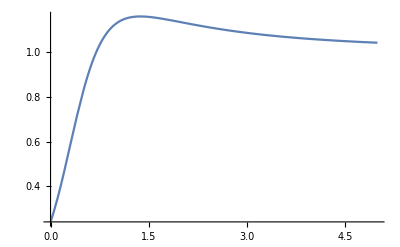

```mathematica
Plot[(40. (2256.+5305. Q+4620. Q^2)^2)/(8.40264369*^8+9.62230872*^8 Q+6.613186*^8 Q^2+1.960728*^9 Q^3+8.53776*^8 Q^4),{Q,0,5},PlotRange->All]
```

```mathematica
NMinimize[-((40. (2256.+5305. Q+4620. Q^2)^2)/(8.40264369*^8+9.62230872*^8 Q+6.613186*^8 Q^2+1.960728*^9 Q^3+8.53776*^8 Q^4)),Q]
```

{-1.15664,{Q→1.37407}}